## §3. Степенные ряды

### 3.1. Область сходимости и свойства степенных рядов.

Ряд

c_0+c_1(z-z_0)+(c_2(z-z_0))^2+...+(c_n(z-z_0))^n+...=∑_(n=0)^∞ (c_n(z-z_0))^n

называется степенным по степенях z-z_0. В частности, ряд

c_0+c_1 z+c_2 z^2+...+c_n z^n+...=∑_(n=0)^∞ c_n z^n

является степенным по степеням z .

Т е о р е м а  А б е л я. Если степенной ряд (2) сходится в точке z=z_1≠ 0, то он абсолютно сходится для всех z таких, что |z|< |z_1|. Если же ряд (2) расходится в точке z=z_2, то он расходится и для всех z таких, что |z| > |z_2|.

Из теоремы Абеля следует, что областью сходимости степенного ряда является круг с центром в начале координат(с центром в точке z_0), радиус которого может быть определен применением либо признака Даламбера, либо признака Коши, т.е. из условий:

lim_(n→∞) |(c_(n+1)z^(n+1))/(c_n z)|=|z|  lim_(n→∞) |(c_(n+1))/c_n|<1

lim_(n→∞) (|c_n z^n|)^(1/n)=|z|lim_(n→∞) (|c_n|)^(1/n)<1

Отсюда для вычисления радиуса R круга сходимости получаем соотношения:

R=1/(lim_(n→∞) (|c_n|)^(1/n))  или    R=1/(lim_(n→∞) |(c_(n+1))/c_n|)

##### Пример №12 .165

Найти область абсолютной сходимости и область равномерной сходимости ряда:

∑_(n=1)^∞ (z-1)^n/(n^2 2^n)

Радиус круга сходимости определим по формуле (5):

```mathematica
R=1/Limit[(1/(n^2 2^n))^(1/n),n-> Infinity]
```

2

Получили, что область абсолютной сходимости исходного ряда: |z-1| <R=2.

На границе имеем:

|(z-1)^n/(n^2 2^n)|≤ 1/(n^2 2^n)

Следовательно, по принзнаку Вейерштрасса, ряд сходится равномерно в области: |z-1|≤ 2

##### Пример №12 .168

Найти область абсолютной сходимости и область равномерной сходимости ряда:

∑_(n=1)^∞ (-1)^(n +1)(2^(n+1)(z-4)^n)/((n+1)√(ln(n+1)))

Запишем общий член:

```mathematica
f[n_,z_]:=(-1)^(n+1)(2^(n+1)(z-4)^n)/((n+1)√Log[n+1])
```

Найдем, при помощи критерия Даламбера, область абсолютной сходимости:

```mathematica
Limit[Abs[f[n+1,z]]/Abs[f[n,z]],n-> Infinity]
```

2 Abs[-4+z]

Получаем, что область сходимости |z-4|<1/2.

На границе сходимости, при z=4.5, имеем:

∑_(n=1)^∞ (2^(n+1)(1/2)^n)/((n+1)√(ln(n+1)))=∑_(n=1)^∞ 2/((n+1)√(ln(n+1)))

Исследуем на сходимость, по интегральному признаку Коши:

```mathematica
Integrate[2/((n+1)√Log[n+1]),{n,1,Infinity}]
```

∫_1^∞ 2/((1+n) √Log[1+n])ⅆn

Получили, что ряд расходится абсолютно, следовательно исходный ряд, равномерно сходится в области |z-4|≤ r<1/2

Исследуем ряды на границе: 1. z=4.5

∑_(n=1)^∞ ((-1)^(n+1) 2)/((n+1)√(ln(n+1)))

Так как ряд не сходится абсолютно, исследуем на условную сходимость:

Общий член ряда:

```mathematica
Limit[2/((n+1)√Log[n+1]),n-> Infinity]
```

0

Стремится к 0.

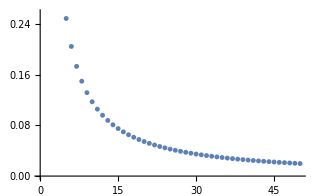

```mathematica
ListPlot[Table[2/((n+1)√Log[n+1]),{n,1,50}]]
```

Члены ряда по модулю убывают, условия критерия Лейбница выполнены, следовательно ряд при z=4.5 сходится условно.

2. z=3.5

∑_(n=1)^∞ ((-1)^(n+1)2^(n+1)(-1/2)^n)/((n+1)√(ln(n+1)))=∑_(n=1)^∞ -2/((n+1)√(ln(n+1)))=-∑_(n=1)^∞ 2/((n+1)√(ln(n+1)))

Ранее было получено, что данный ряд не сходится (см. выше).

##### Пример №12 .174

Найти область абсолютной сходимости и область равномерной сходимости ряда:

∑_(n=1)^∞ ((n!)^2 z^n)/((2n)!)

Запишем общий член ряда:

```mathematica
f[n_,z_]:=(n!)^2/((2n)!)z^n
```

При помощи признака Даламбера, определим область сходимости:

```mathematica
Limit[f[n+1,z]/f[n,z],n->Infinity]
```

z/4

Область сходимости данного ряда |z|<4.

На границе z=4 имеем ряд:

∑_(n=1)^∞ ((n!)^2 4^n)/((2n)!)

Который по интегральному признаку Коши:

```mathematica
Integrate[f[n,4],{n,1,Infinity}]
```

∫_1^∞ (4^n (n!)^2)/((2 n)!)ⅆn

Не сходится.

На границе z=-4, ряд,

∑_(n=1)^∞ (-1)^n((n!)^2 4^n)/((2n)!)

Не удовлетворяет критериям признака Лейбница:

```mathematica
Limit[((n!)^2 4^n)/((2n)!),n-> Infinity]
```

∞

Следовательно, не сходится абсолютно и условно.

Таким образом исходный ряд сходится равномерно на |z|≤ r<4

### 2. Разложение функций в ряд Тейлора.

Т е о р е м а  Т е й л о р а. Функция f(z), аналитичная в круге |z-z_0|<R, однозначно представима в этом круге своим рядом Тейлора

f(z)=∑_(n=0)^∞ (c_n(z-z_0))^n,

коэффициенты которого определяются по формулам:

с_n=(f^(n)(z_0))/(n!)=1/(2π ⅈ)∮_(|z-z_0|=r) (f(z))/(z-z_0)^(n+1)ⅆz,n=0,1...

С л е д с т в и е. Если функция f(z) аналитична в области D и z_0∈D, то в круге |z-z_0|<R(z_0,D), где R(z_0,D) - наименьшее растояние от точки z_0 до границы области D или до ближайшей точки z', в которой f(z) не аналитична, f(z) может быть представлена в виде степенного ряда

f(z)=∑_(n=0)^∞ (f^(n)(z_0))/(n!)(z-z_0)^n

Если z_0=0, то ряд Тейлора также называют рядом Маклорена.

Разложения элементарных функций:

ⅇ^z=1+z+z^2/(2!)+...+z^n/(n!)+...=∑_(n=0)^∞ z^n/(n!),  z∈ℂ

cos z=1-z^2/(2!)+...+(-1)^n z^(2n)/((2n)!)+...=∑_(n=0)^∞ (-1)^n z^(2n)/((2n)!), z∈ℂ

sin z=z-z^3/(3!)+...+(-1)^(n+1)z^(2n+1)/((2n+1)!)+...=∑_(n=0)^∞ (-1)^n z^(2n+1)/((2n+1)!), z∈ℂ

ln(1+z)=z-z^2/2+...+(-1)^(n+1)z^n/n+...=∑_(n=1)^∞ (-1)^(n+1)z^n/n,  |z|<1

arctg z=z-z^3/3+...+(-1)^(n+1)z^(2n+1)/(2n+1)+...=∑_(n=0)^∞ (-1)^(n+1)z^(2n+1)/(2n+1),  |z|<1

(1+z)^a=1+a z+(a(a-1))/(2!)z^2+...+(a(a-1)...(a-n+1))/(n!)z^n=1+∑_(n=1)^∞ Binomial[a,n]/(n!)z^n,  |z|<1

где Binomial[a,n]=a(a-1)...(a-n+1)

1/(1+z)=1-z+z^2+...+(-1)^n z^n=∑_(n=0)^∞ (-1)^n z^n,  |z|<1

##### Пример №12.214

Разложить функцию в ряд по степеням z :

f(z)=e^(-z^2)

Рассмотрим сначала решение данной задачи “в лоб”. Так как данная нам функция аналитична во всей комплексной плоскости, то для разложения функции в ряд применима формула (8).

Запишем заданную функцию:

```mathematica
f[z_]:=Exp[-z^2]
```

Теперь запишем выражение для n-ого коэффициента с_n:

```mathematica
c[n_]:=D[f[z],{z,n}]/n!/.z->0
```

Так как мы вычисляем разложение в ряд Тейлора в окрестности точки 0, то z_0=0. Такой ряд также называют рядом Маклорена.

Для того чтобы получить окончательный ответ, найдем сумму ряда, например до 16 члена:

```mathematica
Sum[c[n] z^n,{n,0,16}]
```

1-z^2+z^4/2-z^6/6+z^8/24-z^10/120+z^12/720-z^14/5040+z^16/40320

Запишем данное выражение в виде функции:

```mathematica
r[z_,k_]:=Sum[c[n] z^n,{n,0,k}]
```

Для того чтобы проверить полученный результат, построим графики функции для исходной функции и ряда до 16 члена:

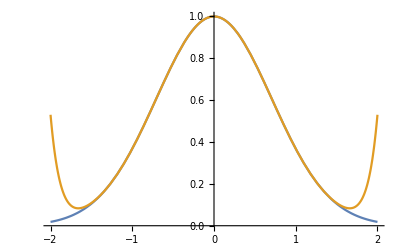

```mathematica
Plot[{f[z],Evaluate@r[z,16]},{z,-2,2},PlotRange->All]
```

Примечание: функция Evaluate здесь используется для того, чтобы сначала получить разложение в ряд Тейлора, а затем в него происходила подстановка значений z отрезка [-2;2].

Увеличивая максимальный порядок разложения, можно добиться сходимости ряда к функции на более широком отрезке.

##### Програмный модуль

Составим учебную программу, которая будет выполнять разложение функции в ряд Тейлора по формуле (8).

Имеем следующую тривиальную последовательность действий:

Пусть задана функция f(z)=cos(z).

```mathematica
f[z_]:=Cos[z]
```

1. Записываем функцию коэффициента:

```mathematica
c[n_,z0_]:=D[f[z],{z,n}]/n!/.z->z0
```

2. Находим сумму:

```mathematica
Sum[c[n,0](z-0)^n,{n,0,8}]
```

1-z^2/2+z^4/24-z^6/720+z^8/40320

Соберем это всё в единый модуль:

```mathematica
seriesO[func_,z_,z0_,k_]:=Module[{coef},
coef[n_]:=D[func,{z,n}]/n!/.z->z0;
Sum[coef[n](z-z0)^n,{n,0,k}]]
```

Продемонстрируем пример:

```mathematica
seriesO[Sin[z]^2,z,0,12]
```

z^2-z^4/3+(2 z^6)/45-z^8/315+(2 z^10)/14175-(2 z^12)/467775

##### Пример №12.242

```mathematica
seriesO[Exp[z^2-4z+1],z,2,12]
```

1/ⅇ^3+(-2+z)^2/ⅇ^3+(-2+z)^4/(2 ⅇ^3)+(-2+z)^6/(6 ⅇ^3)+(-2+z)^8/(24 ⅇ^3)+(-2+z)^10/(120 ⅇ^3)+(-2+z)^12/(720 ⅇ^3)

Напомним, что данный модуль использует формулу (8) для разложения функции в ряд.

Рассмотрим другие пути решения поставленной задачи.

##### Пример №12.231

Используя разложения основных элементарных функций, разложить функцию в ряд по степеням z и указать область сходимости полученного ряда:

f(z)=∫_0^z e^(-t^2/2)ⅆt

На этот раз воспользуемся стандартными разложениями (9)-(15), для того чтобы получить разложение функции в ряд.

Подынтегральная функция - эскпоненциальная, значит используя выражение (9), а также замену h=-t^2/2, получим:

```mathematica
seriesO[Exp[h],h,0,8]/.h->-t^2/2
```

1-t^2/2+t^4/8-t^6/48+t^8/384-t^10/3840+t^12/46080-t^14/645120+t^16/10321920

Теперь требуется лишь проинтегрировать полученное выражение:

```mathematica
Integrate[seriesO[Exp[h],h,0,8]/.h->-t^2/2,{t,0,z}]
```

z-z^3/6+z^5/40-z^7/336+z^9/3456-z^11/42240+z^13/599040-z^15/9676800+z^17/175472640

Получили разложение в ряд Тейлора до 17ого члена исходной функции, причем, так как область сходимости ряда (9) - вся комплексная плоскость, то и областью сходимости полученного ряда также является вся комплексная плоскость.

Примечание: если слегка модифицировать модуль, полученный в предыдущем примере:

```mathematica
seriesO1[func_,z_,z0_,k_]:=Module[{coef,t},
coef[n_]:=D[func[t],{t,n}]/n!/.t->z0;
Sum[coef[n](z-z0)^n,{n,0,k}]]
```

Если записать функцию при помощи безымянной переменной (см. Help -> Slot), например:

```mathematica
f=Exp[#]&;
```

```mathematica
f[z]
```

ⅇ^z

То, получим следующий результат:

```mathematica
seriesO1[Exp[#]&,-t^2/2,0,8]
```

1-t^2/2+t^4/8-t^6/48+t^8/384-t^10/3840+t^12/46080-t^14/645120+t^16/10321920

```mathematica
Integrate[seriesO1[Exp[#]&,-t^2/2,0,8],{t,0,z}]
```

z-z^3/6+z^5/40-z^7/336+z^9/3456-z^11/42240+z^13/599040-z^15/9676800+z^17/175472640

Также вместо безымянной функции, можно использовать просто заголовок подынтегральной функции:

```mathematica
seriesO1[Exp,-t^2/2,0,8]
```

1-t^2/2+t^4/8-t^6/48+t^8/384-t^10/3840+t^12/46080-t^14/645120+t^16/10321920

##### Пример №12.218

Используя разложения основных элементарных функций, разложить функцию в ряд по степеням z и указать область сходимости полученного ряда:

f(z)=(27-z)^(1/3)

Преобразуем выражение:

f(z)=3(1-z/27)^(1/3)

Теперь, пользуясь стандартным разложением (14), при помощи замены t=-z/27, найдем разложение исходной функции в ряд:

При помощи безымянной функции:

```mathematica
seriesO1[3(1+#)^(1/3)&,-z/27,0,6]
```

3-z/27-z^2/2187-(5 z^3)/531441-(10 z^4)/43046721-(22 z^5)/3486784401-(154 z^6)/847288609443

При помощи замены:

```mathematica
seriesO[3(1+t)^(1/3),t,0,6]/.t->-z/27
```

3-z/27-z^2/2187-(5 z^3)/531441-(10 z^4)/43046721-(22 z^5)/3486784401-(154 z^6)/847288609443

Область сходимости ряда определим из:

|t|<1 ⟹|z|<27

##### Встроенные средства

В Wolfram Mathematica функция, которая отвечает за разложение в ряд, она имеет следующую структуру: Series[ f[z], {z, z_0, n}] , где n- порядок разложения. Продемонстрируем пример:

```mathematica
Series[ Cos[z],{z,0,5}]
```

1-z^2/2+z^4/24+O[z]^6

Примечание: O[z]^6 , о-малое от z^6 - остаток ряда.

```mathematica
Series[Exp[-z^2],{z,0,16}]
```

1-z^2+z^4/2-z^6/6+z^8/24-z^10/120+z^12/720-z^14/5040+z^16/40320+O[z]^17

```mathematica
Series[Exp[Cos[z]],{z,0,6}]
```

ⅇ-(ⅇ z^2)/2+(ⅇ z^4)/6-(31 ⅇ z^6)/720+O[z]^7

Для того, чтобы получить n-ый коэффициент разложения, существует функция SeriesCoefficient[ f[z], {z,z_0,n}]. Примеры:

```mathematica
SeriesCoefficient[Exp[-z^2],{z,0,8}]
```

1/24

```mathematica
SeriesCoefficient[(27-z)^(1/3),{z,0,3}]
```

-5/531441

Также есть возьможность получить общий член:

```mathematica
SeriesCoefficient[Log[1+z],{z,0,n}]
```

Piecewise[{{(-1)^(1+n)/n, n≥1}, {0, True}}]

Или если задать, что n>1, можно избавиться от кусочно-заданной функции:

```mathematica
Refine[SeriesCoefficient[Log[1+z],{z,0,n}],n>1]
```

(-1)^(1+n)/n

Следующая конструкция, позволит вывести ответ в формульном виде:

```mathematica
TraditionalForm@Inactivate[Sum[Refine[SeriesCoefficient[Exp[z],{z,0,n}],n>0] z^n, {n,0,Infinity}],Sum]
```

z^n/(n!)n0∞

Где функция Inactivate запрещает функции, следующей за ней (Sum) вычеслять результат, а TraditionalForm преобразует выражение в традиционный вид.

Составим функцию:

```mathematica
seriesF[f_,z_,z0_]:=TraditionalForm@Inactivate[Sum[Refine[SeriesCoefficient[f,{z,z0,n}],n>5 ](z-z0)^n, {n,0,Infinity}],Sum]
```

```mathematica
seriesF[1/(-z+1),z,0]
```

z^nn0∞

Продемонстрируем пример на основе задачи №12.214:

```mathematica
seriesF[Exp[t],t,0]/.t->-z^2
```

((-z^2)^n)/(n!)n0∞

##### Пример №12.232

Разложить функцию в ряд:

f(z)=∫_0^z (sin(t))^2/t ⅆt

Получим разложение подинтегральной функции:

```mathematica
Sin[t]^2/t//TrigReduce
```

(1-Cos[2 t])/(2 t)

Зная стандартное разложение функции cos(h) (10), где h=2t, получаем:

(1-(1-h^2/(2!)+...+(-1)^n h^(2n)/((2n)!)+...))/(2t)=∑_(n=1)^∞ ((-1)^n(2t)^(2n-1))/((2n)!)=∑_(n=1)^∞ ((-1)^n 4^n t^(2n-1))/(2(2n)!)

Теперь, применяя теорему о почленном интегрировании получаем:

∫_0^z ∑_(n=1)^∞ ((-1)^(n+1)4^n t^(2n-1))/(2(2n)!)ⅆt=∑_(n=1)^∞ ((-1)^(n+1)4^n)/(2(2n)!)∫_0^z t^(2n-1)ⅆt=∑_(n=1)^∞ ((-1)^(n+1)4^n z^(2n))/(2(2n)!2n)

В итоге получаем ответ:

f(z)=∫_0^z (sin(t))^2/t ⅆt=∑_(n=1)^∞ ((-1)^(n+1)4^n z^(2n))/(2(2n)!2n),   z∈ℂ.

Проверим полученное аналитическое решение при помощи функции Series:

```mathematica
Series[Integrate[Sin[t]^2/t,{t,0,z}],{z,0,12}]
```

z^2/2-z^4/12+z^6/135-z^8/2520+z^10/70875-z^12/2806650+O[z]^13

```mathematica
Sum[((-1)^(n+1)4^n z^(2n))/(2(2n)!2n),{n,1,6}]
```

z^2/2-z^4/12+z^6/135-z^8/2520+z^10/70875-z^12/2806650

Ряды совпадают, следовательно получили правильный ответ.

##### Пример №12.237

Разложить функцию в ряд по степеням z-z_0 и опредить область сходимости полученного ряда:

f(z)=1/(1-z), z_0=3ⅈ

Получим разложение, воспользовавшись опцией Series:

```mathematica
Series[1/(1-z),{z,3I,6}]
```

(1/10+(3 ⅈ)/10)-(2/25-(3 ⅈ)/50) (z-3 ⅈ)-(13/500+(9 ⅈ)/500) (z-3 ⅈ)^2+(7/2500-(6 ⅈ)/625) (z-3 ⅈ)^3+(79/25000-(3 ⅈ)/25000) (z-3 ⅈ)^4+(11/31250+(117 ⅈ)/125000) (z-3 ⅈ)^5-(307/1250000-(249 ⅈ)/1250000) (z-3 ⅈ)^6+O[z-3 ⅈ]^7

Также можно воспользоваться созданным ранее модулем seriesO:

```mathematica
seriesO[1/(1-z),z,3I,6]
```

(1/10+(3 ⅈ)/10)-(2/25-(3 ⅈ)/50) (-3 ⅈ+z)-(13/500+(9 ⅈ)/500) (-3 ⅈ+z)^2+(7/2500-(6 ⅈ)/625) (-3 ⅈ+z)^3+(79/25000-(3 ⅈ)/25000) (-3 ⅈ+z)^4+(11/31250+(117 ⅈ)/125000) (-3 ⅈ+z)^5-(307/1250000-(249 ⅈ)/1250000) (-3 ⅈ+z)^6

Запишем ответ в стандартном виде:

```mathematica
seriesF[1/(1-z),z,3I]
```

(1+3 ⅈ)^(n+1) 10^(-n-1) (z-3 ⅈ)^nn0∞

Область сходимости определим при помощи функции SumConvergence:

```mathematica
SumConvergence[(1+3 I)^(1+n) 10^(-1-n) (-3 I+z)^n,n]
```

√10 Abs[-3 ⅈ+z]<10

В итоге имеет ответ:

1/(1-z)=∑_(n=0)^∞ (1+3ⅈ)^(n+1)/10^(n+1)(z-3ⅈ)^n,  |z-3ⅈ|<√10

##### Пример №12.250

Найти область сходимости указанного ряда и его сумму:

∑_(n=0)^∞ (-1)^n a^(-2n-2)z^(2n), a≠ 0

Для того чтобы найти сумму, преобразуем выражение к:

1/a^2∑_(n=0)^∞ (-1)^n((z/a)^2)^n, a≠ 0

Суммой данной геометрической прогрессии является следующая функция:

1/(1+η)=∑_(n=0)^∞ (-1)^n η^n, где η=(z/a)^2

Область сходимости данной суммы |η|<1

Проверим себя:

```mathematica
Sum[(-1)^n a^(-2n-2)z^(2n),{n,0,Infinity}]
```

1/(a^2+z^2)

Получили тот же самый результат.

Следовательно, получаем ответ:

∑_(n=0)^∞ (-1)^n a^(-2n-2)z^(2n)=1/a^2 1/(1+z^2/a^2)=1/(a^2+z^2), |z|< |a|